```mathematica
list={{{-34.6077,-58.692},1},{{-23.5727,-46.65},2},{{6.3155,-75.9408},3},{{-16.6438,-68.451},4},{{-02.0426,-60.092},5},{{-53.092,-72.04}},6}
```

{{{-34.6077,-58.692},1},{{-23.5727,-46.65},2},{{6.3155,-75.9408},3},{{-16.6438,-68.451},4},{{-2.0426,-60.092},5},{{-53.092,-72.04}},6}

```mathematica
llist=Table[list[[i,1]],{i,1,6}]
```

{{-34.6077,-58.692},{-23.5727,-46.65},{6.3155,-75.9408},{-16.6438,-68.451},{-2.0426,-60.092},{-53.092,-72.04}}

```mathematica
A=GeoGraphics[{Table[GeoStyling[
    Directive[Opacity[0.2+0.4i], EdgeForm[Hue[0.1 i]],{ Hue[0.5 i]}]],{i,1,6}],MapThread[GeoDisk,{llist,R}]},GeoRange->{{-60,15},{-100,-15}},GeoProjection->"Mercator",GeoGridLines->Quantity[5,"AngularDegrees"],GeoBackground->"ContourMap"];
```

```mathematica
B=GeoGraphics[{GeoStyling[
    Directive[Opacity[0.3], EdgeForm[Blue],Red]],
MapThread[GeoDisk,{llist,R}]},
GeoRange->{{-60,15},{-100,-15}},
GeoProjection->"Mercator",
GeoGridLines->Quantity[10,"AngularDegrees"],
GeoBackground->"ReliefMap"];
```

```mathematica
R=Table[Quantity[i,"Kilometers"],{i,300,305,1}];
```

```mathematica
R={Quantity[659,"Kilometers"],Quantity[550,"Kilometers"],Quantity[559,"Kilometers"],Quantity[359,"Kilometers"],Quantity[659,"Kilometers"],Quantity[659/1.5,"Kilometers"]};
```

```mathematica
data=Transpose[{llist,R}];
```

```mathematica
LRLPZ={54,38,47}
```

{54,38,47}

```mathematica
Mean[LRLPZ]//N
```

46.3333

```mathematica
GeoGraphics[{
GeoStyling[
Directive[Opacity[0.3],EdgeForm[Blue],Red]],
GeoCircle@@@data},(*EDIT:shorter form*)
(*GeoDisk[#[[1]],#[[2]]]&/@data},*)
GeoRange->{{-60,15},{-100,-15}},
(*GeoProjection->"Mollweide",*)
GeoGridLines->Quantity[5,"AngularDegrees"],
GeoBackground->"ContourMap"];
```

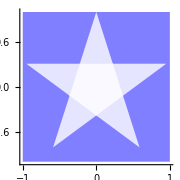

```mathematica
Show[lonestar=Graphics[GraphicsGroup[{EdgeForm[],Blue,Opacity[.5],Polygon[{{-1,-1},{1,-1},{1,1},{-1,1}}],White,Opacity[.8],Polygon[Table[Through[{Sin,Cos}[4 π k/5]],{k,5}]],Polygon[Table[{1,-1}/GoldenRatio^2 Through[{Sin,Cos}[2 π k/5]],{k,5}]]}]],Axes->True,ImageSize->Small]
```

```mathematica
RR={550,500,670,460,650,500}
```

{550,500,670,460,650,500}

```mathematica
{550,500,670,455,320,400}
```

```mathematica
TURN=Max[RR]-Mean[RR]//N
```

115.

```mathematica
RRR=Abs[(RR-TURN)]/Max[RR]//N
```

{0.649254,0.574627,0.828358,0.514925,0.798507,0.574627}

```mathematica
c=Table[Blend[{Blue,Red},RRR[[i]]],{i,1,6}]
```

{RGBColor[0.6492537313432836, 0., 0.35074626865671643],RGBColor[0.5746268656716418, 0., 0.4253731343283582],RGBColor[0.8283582089552239, 0., 0.17164179104477606],RGBColor[0.5149253731343284, 0., 0.4850746268656716],RGBColor[0.7985074626865671, 0., 0.20149253731343286],RGBColor[0.5746268656716418, 0., 0.4253731343283582]}

```mathematica
Sort[c]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

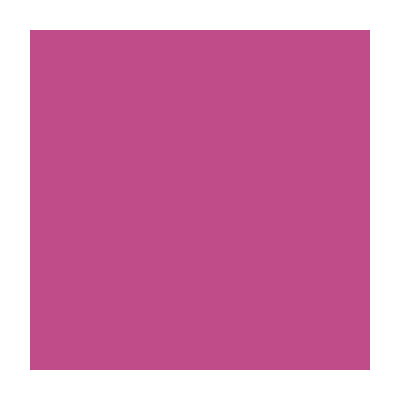
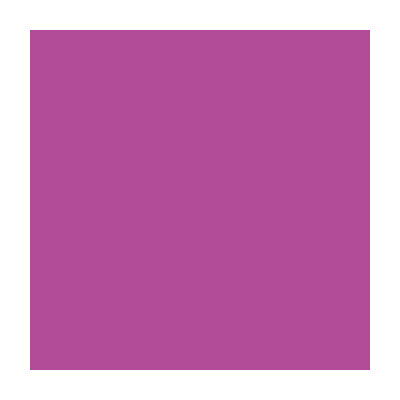
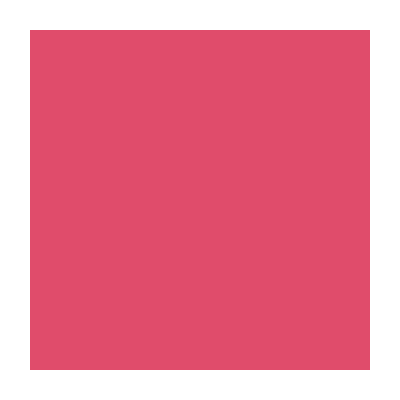
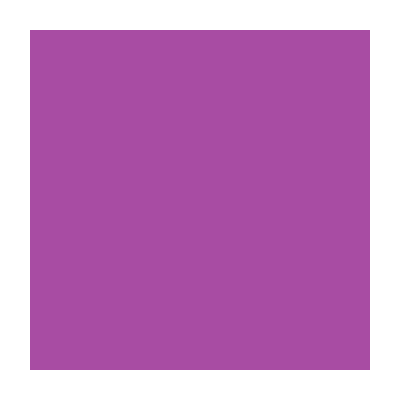
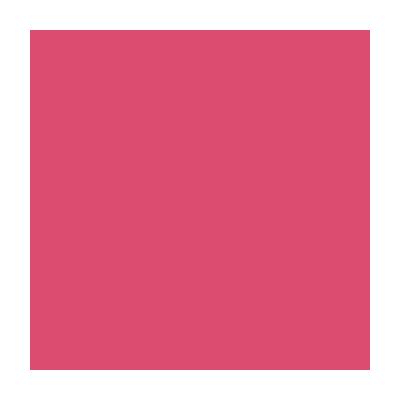
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
circles=Table[Graphics[{c[[i]],Opacity[0.7],Disk[{0,0},Scaled[1.9]],White,Disk[{0,0},1]}],{i,1,6}]
```

```mathematica
Graphics[{FaceForm[Pink],EdgeForm[Directive[Dashed,Opacity[0.9]]],Opacity[0.1],Disk[{0,0},Scaled[1.25]]}];
```

```mathematica
RR={550,450,400,430,320,420}
```

{550,450,400,430,320,420}

```mathematica
smooth2[a_,R_: 1,n_: 100,hue_: Hue[.25]]:=Graphics@Table[{Blend[{White,hue},Rescale[r,{R,R/n},{0,1}]^a],Disk[{0,0},r]},{r,R,R/n,-R/n}]

blui=Table[smooth2/@{RRR[[i]]+1/9},{i,1,6}]
```

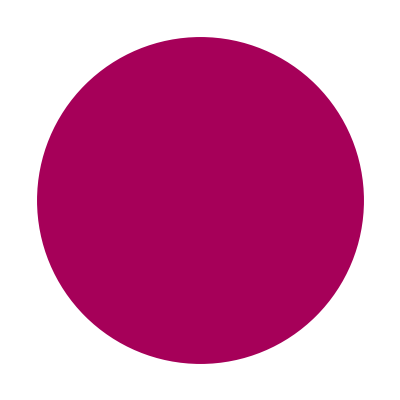
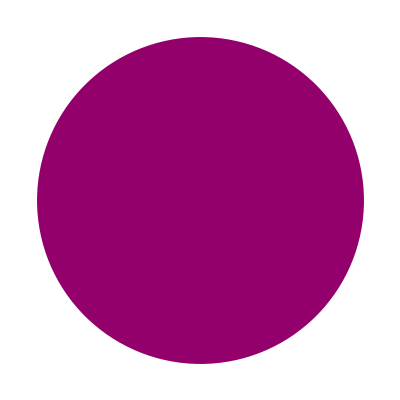
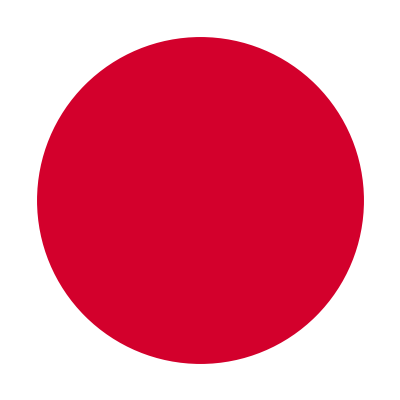
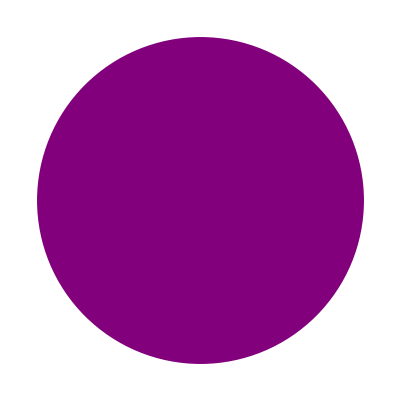
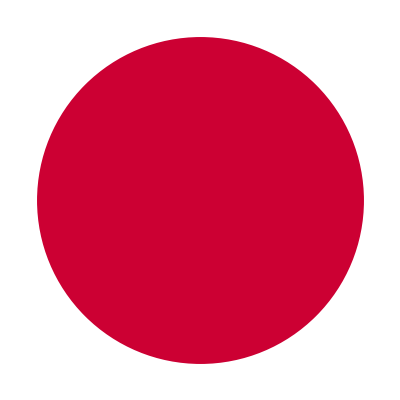
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
circo=Table[Graphics[{c[[i]],Disk[{0,0},i]}],{i,1,6}]
```

```mathematica
data1=Transpose[{llist,circo}];
```

```mathematica
LRT=Legended[GeoGraphics[{EdgeForm[Black],Polygon[LinguisticAssistant],Polygon[LinguisticAssistant],Polygon[LinguisticAssistant],Polygon[LinguisticAssistant],Polygon[LinguisticAssistant]
(*GeoMarker[llist,circles,"]Alignment"->Center]}*),(*EDIT:shorter form*)
GeoMarker[#[[1]],#[[2]]]&/@data1},
GeoRange->{{-60,15},{-100,-15}},
(*GeoProjection->"Mollweide",*)
GeoGridLines->Quantity[5,"AngularDegrees"],
GeoBackground->Automatic,ImageSize-> 800],
Placed[BarLegend[{Sort[c],{45,70}},LegendLayout->"Row",LegendLabel->"Lidar Ratio",LegendMargins->3,LegendFunction-> Framed,LabelStyle->Directive[Blue,Bold,FontFamily->"Helvetica",Large]],Below
]]
```

-Graphics-

```mathematica
Export["LR2a.jpg",LRT,ImageResolution ->300]
```

LR2a.jpg